```mathematica
unitCell[x_,y_]:={Red,Disk[{x,y},0.1],Blue,Disk[{x,y+2/3 Sin[120 Degree]},0.1],Gray,
,Line[{{x,y},{x,y+2/3 Sin[120 Degree]}}],Line[{{x,y},{x+Cos[30 Degree]/2,y-Sin[30 Degree]/2}}],Line[{{x,y},{x-Cos[30 Degree]/2,y-Sin[30 Degree]/2}}]}
```

```mathematica
Graphics[unitCell[0,0],ImageSize->100]
```

-Graphics-

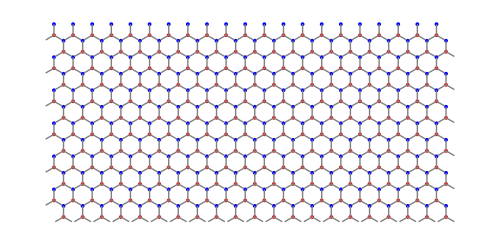

```mathematica
grid = Graphics[Block[{unitVectA={Cos[120 Degree],Sin[120 Degree]},unitVectB={1,0}},Table[unitCell@@(unitVectA j+unitVectB k),{j,1,12},{k,Ceiling[j/2],20+Ceiling[j/2]}]],ImageSize->500]
```

```mathematica
{width,height}=ImageDimensions[grid];
w=40;h=45;
grid=ImageTake[grid,{h,height-h},{w,width-w}];
ParametricPlot3D[{Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]},{u,0,2 Pi},{v,0,Pi},Mesh->None,PlotPoints->100,TextureCoordinateFunction->({#4,1-#5}&),Boxed->False,PlotStyle->Texture[Show[grid,ImageSize->1000]],Lighting->"Neutral",Axes->False,RotationAction->"Clip",ViewPoint->{-2.026774,2.07922,1.73753418},ImageSize->600]
```

-Graphics3D-

```mathematica
Graphics3D[Point[SpherePoints[20]]]
```

-Graphics3D-

```mathematica
points = SpherePoints[20]
```

{{-0.187592,-0.57735,-0.794654},{-0.187592,0.57735,-0.794654},{0.187592,-0.57735,0.794654},{0.187592,0.57735,0.794654},{-0.607062,0.,-0.794654},{0.607062,0.,0.794654},{-0.303531,-0.934172,-0.187592},{-0.303531,0.934172,-0.187592},{0.303531,-0.934172,0.187592},{0.303531,0.934172,0.187592},{-0.491123,-0.356822,0.794654},{-0.491123,0.356822,0.794654},{0.491123,-0.356822,-0.794654},{0.491123,0.356822,-0.794654},{-0.794654,-0.57735,0.187592},{-0.794654,0.57735,0.187592},{0.794654,-0.57735,-0.187592},{0.794654,0.57735,-0.187592},{-0.982247,0.,-0.187592},{0.982247,0.,0.187592}}

```mathematica
Circle[%, 10]
```

```mathematica
Circle[Point[{{-0.1875924740850799,-0.5773502691896257,-0.7946544722917661},{-0.1875924740850799,0.5773502691896257,-0.7946544722917661},{0.1875924740850799,-0.5773502691896257,0.7946544722917661},{0.1875924740850799,0.5773502691896257,0.7946544722917661},{-0.6070619982066862,0.,-0.7946544722917661},{0.6070619982066862,0.,0.7946544722917661},{-0.3035309991033431,-0.9341723589627157,-0.1875924740850799},{-0.3035309991033431,0.9341723589627157,-0.1875924740850799},{0.3035309991033431,-0.9341723589627157,0.1875924740850799},{0.3035309991033431,0.9341723589627157,0.1875924740850799},{-0.49112347318842303,-0.35682208977308993,0.7946544722917661},{-0.49112347318842303,0.35682208977308993,0.7946544722917661},{0.491123473188423,-0.35682208977308993,-0.7946544722917661},{0.491123473188423,0.35682208977308993,-0.7946544722917661},{-0.7946544722917661,-0.5773502691896257,0.1875924740850799},{-0.7946544722917661,0.5773502691896257,0.1875924740850799},{0.7946544722917661,-0.5773502691896257,-0.1875924740850799},{0.7946544722917661,0.5773502691896257,-0.1875924740850799},{-0.9822469463768461,0.,-0.1875924740850799},{0.9822469463768461,0.,0.1875924740850799}}],10]
```

Circle[Point[{{-0.187592,-0.57735,-0.794654},{-0.187592,0.57735,-0.794654},{0.187592,-0.57735,0.794654},{0.187592,0.57735,0.794654},{-0.607062,0.,-0.794654},{0.607062,0.,0.794654},{-0.303531,-0.934172,-0.187592},{-0.303531,0.934172,-0.187592},{0.303531,-0.934172,0.187592},{0.303531,0.934172,0.187592},{-0.491123,-0.356822,0.794654},{-0.491123,0.356822,0.794654},{0.491123,-0.356822,-0.794654},{0.491123,0.356822,-0.794654},{-0.794654,-0.57735,0.187592},{-0.794654,0.57735,0.187592},{0.794654,-0.57735,-0.187592},{0.794654,0.57735,-0.187592},{-0.982247,0.,-0.187592},{0.982247,0.,0.187592}}],10]

```mathematica
circle3D[centre_: {0,0,0},radius_: 1,normal_: {0,0,1},angle_: {0,2 Pi}]:=Composition[Line,Map[RotationTransform[{{0,0,1},normal},centre],#]&,Map[Append[#,Last@centre]&,#]&,Append[DeleteDuplicates[Most@#],Last@#]&,Level[#,{-2}]&,MeshPrimitives[#,1]&,DiscretizeRegion,If][First@Differences@angle≥2 Pi,Circle[Most@centre,radius],Circle[Most@centre,radius,angle]]
```

```mathematica
Graphics3D[Map[circle3D[#,2] &,  points]]
```

-Graphics3D-

```mathematica
points = SpherePoints[20]
```

{{-0.187592,-0.57735,-0.794654},{-0.187592,0.57735,-0.794654},{0.187592,-0.57735,0.794654},{0.187592,0.57735,0.794654},{-0.607062,0.,-0.794654},{0.607062,0.,0.794654},{-0.303531,-0.934172,-0.187592},{-0.303531,0.934172,-0.187592},{0.303531,-0.934172,0.187592},{0.303531,0.934172,0.187592},{-0.491123,-0.356822,0.794654},{-0.491123,0.356822,0.794654},{0.491123,-0.356822,-0.794654},{0.491123,0.356822,-0.794654},{-0.794654,-0.57735,0.187592},{-0.794654,0.57735,0.187592},{0.794654,-0.57735,-0.187592},{0.794654,0.57735,-0.187592},{-0.982247,0.,-0.187592},{0.982247,0.,0.187592}}

```mathematica
tocartesian=CoordinateTransformData["Spherical"->"Cartesian","Mapping"];
spherecentre={0,0,0};
sphereradius=2;
dotsize=0.05;
randcirc:=Module[{circleradius,randompoint},
circleradius=0.8;
randompoint=With[{points=20,samples=40000,iterations=20},Nest[With[{randoms=Join[#,RandomPoint[Sphere[],samples]]},Normalize@Mean@randoms[[#]]&/@Values@PositionIndex@Nearest[#,randoms]]&,RandomPoint[Sphere[],points],iterations]];
{Blue,Sphere[randompoint,dotsize],circle3D[spherecentre+Sqrt[sphereradius^2-circleradius^2] Normalize[randompoint-spherecentre],circleradius,randompoint-spherecentre]}];
Graphics3D[{{Opacity[0.3,LightGray],Sphere[spherecentre,sphereradius]},Thick,Table[randcirc,{10}]},Boxed->False]
```

Thread::tdlen: Objects of unequal length in {{0.220001,-0.308434,-0.925455},{-0.0936824,-0.948513,0.302566},«16»,{-0.996965,-0.0619151,0.0472022},{0.681063,0.292493,-0.671268}}+{0,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {0,0,0}+{{0.220001,-0.308434,-0.925455},{-0.0936824,-0.948513,0.302566},«16»,{-0.996965,-0.0619151,0.0472022},{0.681063,0.292493,-0.671268}} cannot be combined.

Thread::tdlen: Objects of unequal length in {{0.220001,-0.308434,-0.925455},{-0.0936824,-0.948513,0.302566},«16»,{-0.996965,-0.0619151,0.0472022},{0.681063,0.292493,-0.671268}}+{0,0,0} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

-Graphics3D-

```mathematica
randompoint=TranslationTransform[spherecentre][tocartesian[{sphereradius,RandomReal[{0,Pi}],RandomReal[{0,2 Pi}]}]]
```

{0.5129,1.60639,0.792327}

```mathematica
circleradius=RandomReal[{dotsize,sphereradius}]
```

1.0077

```mathematica
With[{points=20,samples=40000,iterations=20},Nest[With[{randoms=Join[#,RandomPoint[Sphere[],samples]]},Normalize@Mean@randoms[[#]]&/@Values@PositionIndex@Nearest[#,randoms]]&,RandomPoint[Sphere[],points],iterations]]
```

{{0.725912,0.676953,0.121605},{0.636086,-0.668948,-0.384583},{0.525586,-0.213886,0.823415},{0.167692,-0.421432,-0.891221},{-0.0371182,0.806007,0.59074},{0.849805,-0.52692,0.0136671},{-0.25898,0.119983,-0.958402},{-0.705519,-0.265885,0.656924},{0.482528,0.264248,0.835069},{0.377312,0.492551,0.784238},{0.107112,0.843381,-0.526532},{-0.30855,-0.714437,0.627994},{0.100714,-0.98592,-0.133487},{-0.318153,0.710277,0.627922},{0.431114,-0.807865,-0.401864},{-0.78568,0.525093,-0.327084},{-0.942067,0.0628758,0.329479},{0.251455,-0.921569,0.295772},{-0.472281,0.872738,0.123607},{-0.818915,0.395431,0.415949},{-0.678806,-0.594137,-0.431537},{-0.617601,0.705777,0.347056},{0.524292,-0.820375,0.228259},{0.956655,0.0519755,-0.286549},{0.212315,0.657097,-0.723288},{-0.248757,-0.520442,0.81686},{0.490504,-0.629571,0.602533},{0.0749674,-0.98911,0.126653},{-0.0471598,0.552391,-0.83225},{-0.339392,0.513621,0.78804},{0.490983,0.841332,0.226044},{0.102635,-0.30697,0.946169},{0.636117,-0.656564,0.405314},{0.0584419,-0.796892,-0.601288},{0.117685,0.107634,0.987201},{0.400606,-0.0227872,-0.915967},{0.845502,-0.450985,0.285899},{-0.359527,-0.924802,-0.124426},{-0.747238,-0.64852,0.145111},{0.213536,-0.706951,0.674257},{0.10273,0.8926,0.438989},{-0.0876538,-0.840812,0.534183},{0.496439,-0.86799,0.0118949},{0.1534,-0.852088,0.500415},{-0.060523,0.657289,0.751204},{-0.775699,0.243365,0.582293},{-0.972774,-0.219033,0.0757333},{0.526308,-0.621197,-0.580615},{-0.0556312,-0.605097,-0.794206},{0.714304,-0.168683,0.679202},{-0.0998316,-0.0921833,-0.990725},{0.14276,0.0380692,-0.989025},{-0.265149,0.964044,0.0177629},{-0.69401,0.267178,-0.668555},{0.143052,0.979617,-0.141022},{0.348259,0.914026,-0.208019},{0.947184,0.0126526,0.320442},{-0.626349,0.685958,-0.370334},{-0.424357,0.811532,-0.401668},{-0.521375,-0.541023,-0.659896},{-0.888343,-0.256713,0.380718},{-0.490278,0.6409,-0.590656},{-0.949318,-0.216296,-0.228059},{0.151521,0.559652,0.814758},{0.73909,0.355553,0.572126},{-0.0263016,-0.918371,-0.394845},{0.221066,0.729603,0.647155},{0.0574797,-0.514753,0.855409},{0.59509,-0.392463,0.701313},{0.707112,-0.484678,0.514859},{-0.537627,-0.664019,0.51965},{0.945994,-0.321621,0.040676},{-0.955808,0.0082713,-0.293874},{-0.507794,0.147211,-0.848807},{0.803128,0.482959,-0.348908},{0.426421,0.446807,-0.786466},{-0.552587,-0.783973,0.282902},{0.55652,-0.802648,-0.214574},{0.769182,-0.216665,-0.601179},{0.732425,-0.653636,0.190562},{-0.704896,0.015949,-0.709132},{0.995683,-0.0740893,0.0559173},{0.824592,-0.284462,0.489009},{0.851781,0.251803,-0.459417},{0.337841,-0.925378,-0.171867},{0.469132,0.651878,0.595793},{-0.274858,-0.609622,-0.743515},{0.3597,-0.546966,0.755939},{0.549737,0.0167749,0.83517},{-0.673444,0.732914,0.0964948},{-0.999117,0.0283523,0.0310175},{0.413688,-0.7935,0.446341},{0.937376,-0.212976,0.275621},{-0.849245,0.107352,-0.51697},{0.580177,0.814287,-0.018204},{-0.58524,0.553688,0.592389},{0.723362,0.156667,-0.672461},{0.889232,0.332025,0.314684},{0.593374,0.712644,0.374227},{-0.179144,-0.787106,-0.59023},{-0.897822,0.41941,-0.134202},{0.377742,0.789552,-0.483651},{-0.674492,0.482114,-0.55913},{-0.143333,-0.971827,-0.187106},{0.98663,0.149579,-0.0647101},{-0.836042,-0.154548,-0.526449},{-0.738096,-0.658101,-0.148718},{0.32842,-0.379524,0.864929},{-0.791578,0.550592,0.265052},{0.840011,0.536386,-0.0816828},{0.266724,0.926246,0.26632},{0.603351,-0.382757,-0.699617},{-0.167436,0.885858,0.432691},{-0.734743,-0.501204,0.457107},{0.79553,0.532683,0.288757},{-0.0721501,-0.948457,0.308584},{0.891175,-0.398512,-0.216782},{-0.0909808,0.439246,0.893748},{0.138558,-0.211415,-0.967525},{0.752184,-0.453894,-0.477703},{0.915483,0.395525,0.0738278},{-0.421434,0.796173,0.434169},{-0.504151,-0.445924,0.739584},{-0.96448,0.219028,-0.147667},{-0.203984,-0.300493,0.931716},{0.208238,0.330361,0.920597},{0.922956,0.329095,-0.19962},{-0.358032,-0.139063,-0.923296},{0.390131,-0.522952,-0.757838},{-0.316075,0.926268,-0.205241},{0.393457,0.919041,0.0235638},{-0.824736,-0.0318354,0.564622},{-0.679366,-0.338693,-0.650961},{-0.429753,-0.734276,-0.525501},{0.714821,0.13936,0.68528},{-0.089837,0.228636,0.969358},{-0.043906,-0.693321,0.71929},{0.171546,-0.623753,-0.762564},{0.644011,0.643273,-0.414064},{0.895313,-0.2136,-0.390883},{-0.298776,0.922322,0.245063},{-0.309232,-0.856266,0.413744},{-0.0565657,0.998318,-0.0127109},{0.843724,0.00555563,-0.536748},{0.534413,0.199342,-0.82138},{-0.27222,0.754245,-0.597504},{-0.13493,-0.349664,-0.927108},{0.35649,0.819798,0.448157},{0.179688,0.981281,0.0692765},{0.843866,-0.0315486,0.535626},{-0.49542,0.409737,-0.765947},{0.716906,0.679262,-0.157001},{-0.0225245,0.249678,-0.968067},{-0.0206697,0.971475,0.236239},{0.662568,0.420494,-0.61983},{-0.236188,0.372314,-0.897551},{-0.574778,0.337946,0.745267},{0.295559,-0.952055,0.0789651},{-0.86303,0.308423,-0.400069},{0.0109419,-0.103466,0.994573},{-0.403642,-0.377148,-0.833566},{0.422582,-0.280697,-0.861762},{-0.823837,-0.39102,-0.41036},{0.682245,-0.731117,-0.00305548},{-0.460577,-0.182185,0.868722},{-0.0660236,0.961157,-0.267987},{0.281505,0.232767,-0.9309},{0.300748,-0.737706,-0.604434},{0.972199,-0.165839,-0.165307},{-0.355935,-0.922162,0.151422},{-0.849649,0.525874,0.039412},{-0.256744,-0.0062512,0.966459},{-0.139746,-0.988873,0.0509981},{-0.162465,0.879032,-0.448227},{0.584006,0.433459,0.686331},{-0.0309038,0.737602,-0.674529},{0.858165,0.19744,0.473889},{-0.292313,-0.880717,-0.37268},{-0.533417,0.832667,-0.148767},{-0.883586,-0.451422,-0.124476},{-0.575154,-0.818044,0.00174734},{-0.543287,-0.787112,-0.292053},{0.343386,0.102399,0.933595},{0.542127,0.795539,-0.270584},{-0.58013,-0.156692,-0.79931},{0.20578,-0.899678,-0.385013},{0.296067,-0.140127,0.944833},{0.16588,0.434791,-0.885122},{-0.723917,0.676425,-0.135623},{0.680326,0.546863,0.487952},{0.9723,0.169401,0.161046},{0.627855,-0.0835055,-0.773838},{-0.939157,0.301988,0.163667},{0.487794,0.620365,-0.614169},{-0.876333,-0.447766,0.177614},{0.768425,-0.60268,-0.215171},{-0.375587,0.220193,0.90025},{-0.294791,0.578131,-0.76083},{-0.620371,0.0494574,0.782748},{0.180259,0.917241,-0.355211}}

```mathematica
Permutations[{1,0,0}]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
Permutations[{-1, 0, 0}]
```

{{-1,0,0},{0,-1,0},{0,0,-1}}

```mathematica
fn=#~Permute~AlternatingGroup[Length@#]&;

fn@{PlusMinus[1], PlusMinus[τ], PlusMinus[τ']}
```

{{±1,±(1/2 (1+√5)),±(1/2 (1-√5))},{±(1/2 (1+√5)),±(1/2 (1-√5)),±1},{±(1/2 (1-√5)),±1,±(1/2 (1+√5))}}

```mathematica
τ = 1/2(1+Sqrt[5])
τ' = 1/2(1-Sqrt[5])
```

1/2 (1+√5)

1/2 (1-√5)

```mathematica
Graphics3D[Point[pointlist]]
Table[Graphics3D[{Yellow,Opacity[.8],PolyhedronData[p,"GraphicsComplex"]}],{p,{"Icosahedron"}}]
```

-Graphics3D-

{-Graphics3D-}

```mathematica
pointlist = {{1,0,0},{0,1,0},{0,0,1}, {-1,0,0},{0,-1,0},{0,0,-1}, {1,(1/2 (1+√5)),(1/2 (1-√5))}, {-1,-(1/2 (1+√5)),-(1/2 (1-√5))},{(1/2 (1+√5)),(1/2 (1-√5)),1}, {-(1/2 (1+√5)),-1/2( (1-√5)),-1}, {(1/2 (1-√5)),1,(1/2 (1+√5))}, {(-1/2 (1-√5)),-1,-(1/2 (1+√5))}}
```

{{1,0,0},{0,1,0},{0,0,1},{-1,0,0},{0,-1,0},{0,0,-1},{1,1/2 (1+√5),1/2 (1-√5)},{-1,1/2 (-1-√5),1/2 (-1+√5)},{1/2 (1+√5),1/2 (1-√5),1},{1/2 (-1-√5),1/2 (-1+√5),-1},{1/2 (1-√5),1,1/2 (1+√5)},{1/2 (-1+√5),-1,1/2 (-1-√5)}}

```mathematica
ListPlot3D[{SpherePoints[12]}, Mesh->All]
```

-Graphics3D-

```mathematica
Graphics3D[Point[SpherePoints[12]]]
```

-Graphics3D-

```mathematica
DelaunayMesh[SpherePoints[20]]
```

-Graphics3D-

```mathematica
c2 ={{-1,0,0},{0,-1,0},{0,0,1}};
c3 = 1/2{{1-τ,-τ, 1}, {τ, -1, 1-τ}, {1, τ-1, τ}};
c3' = 1/2{{1-τ, -τ, -1}, {τ, -1, τ-1}, {-1, 1-τ, τ}};
c5 = 1/2{{τ-1, -τ, 1}, {τ, 1, τ-1}, {-1, τ-1, τ}};
```

{{1/2 (-1+1/2 (1+√5)),1/4 (-1-√5),1/2},{1/4 (1+√5),1/2,1/2 (-1+1/2 (1+√5))},{-1/2,1/2 (-1+1/2 (1+√5)),1/4 (1+√5)}}

```mathematica
Reduce[
{Abs[c5*r-r]==Abs[c2*r-c5*r], 
Abs[c5*r-r]*τ == Abs[c2*r-r]}, r, Complexes]
```

x==0&&y==0&&z==0

```mathematica
Solve[x==0&&y==0&&z==0,{x,y,z}]
```

{{x→0,y→0,z→0}}

x→0 | y→0 | z→0